```mathematica
(***********
圆柱热源侧面f1与底面f2过余温度函数：
************)
Clear["`*"];
```

```mathematica
(* soil paras *)
k=3.15;
rho=1600;
cp=1400;
a=k/(rho*cp);
(* basis func *)
ftz[h_,z_,t_,t2_]:=1/(t-t2)*(Erf[(h-z)/(2*Sqrt[a*(t-t2)])]+2*Erf[(z)/(2*Sqrt[a*(t-t2)])]-Erf[(h+z)/(2*Sqrt[a*(t-t2)])])
ftr[r0_,r_,t_,t2_]:=BesselI[0,r0*r/(2*a*(t-t2))]*Exp[-(r0^2+r^2)/(4*a*(t-t2))]
fqr[r0_,r_,t_,t2_]:=1/(2*a*(t-t2))*Exp[-(r^2+r0^2)/(4*a*(t-t2))]*(-r0*BesselI[1,r*r0/(2*a*(t-t2))]+r*BesselI[0,r*r0/(2*a*(t-t2))])
(* temp func: 0-t*)
ftwall[r0_,h_,r_,z_,t_,qs_]:=qs*NIntegrate[r0/(4*k)*ftr[r0,r,t,t2]*ftz[h,z,t,t2],{t2,0,t},AccuracyGoal->5]
(* heat flux func: 0-t *)
fqwall[r0_,h_,r_,z_,t_,qs_]:=qs*NIntegrate[r0/4*fqr[r0,r,t,t2]*ftz[h,z,t,t2],{t2,0,t},AccuracyGoal->5]
(* temp bottom func *)
ftbr[r_,r2_,t_,t2_]:=r2/(t-t2)^1.5*BesselI[0,r*r2/(2*a*(t-t2))]*Exp[-(r^2+r2^2)/(4*a*(t-t2))]
ftbz[h_,z_,t_,t2_]:=Exp[-((z-h)^2)/(4*a*(t-t2))]-Exp[-((z+h)^2)/(4*a*(t-t2))]
ftbottom[r0_,h_,r_,z_,t_,qs_]:=qs*(1/(2*k*(Pi*a)^0.5))*NIntegrate[ftbr[r,r2,t,t2]*ftbz[h,z,t,t2],{r2,0,r0},{t2,0,t}]
fqbz[h_,z_,t_,t2_]:=Exp[-((z-h)^2)/(4*a*(t-t2))]*(h-z)/(2*a(t-t2))-Exp[-((z+h)^2)/(4*a*(t-t2))]*(h+z)/(2*a(t-t2))
fqbottom[r0_,h_,r_,z_,t_,qs_]:=qs*(-1/(2*(Pi*a)^0.5))*NIntegrate[ftbr[r,r2,t,t2]*fqbz[h,z,t,t2],{r2,0,r0},{t2,0,t},Method->"CartesianRule"]
```

```mathematica
(***********
f1,f2简单测试案例：
*************)
```

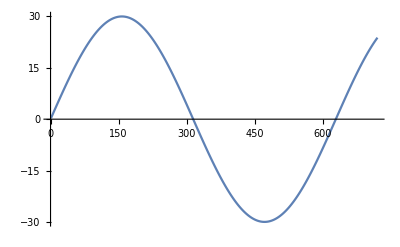

```mathematica
(* borehole paras *)
h=20;
(*r0h=0.1;
r0=r0h*h;*)
r0=10;
qsw=30;(*W/m2*)
qsb=30;
(* calcu paras *)
dt=3600*1; (*s*)
tend=3600*24*30; (*s*)
nt=Floor[tend/dt]; (* 时间节点数*)
mt=500;
magw=5;
magb=5;
qswlist0=Table[qsw*Sin[0.01*it],{it,1,nt}];
qsblist0=Table[qsb+magb*Sin[0.1*it],{it,1,nt}];
ListLinePlot[qswlist0]
```

```mathematica
(* method_1: FCS *)
{r,z}={5,20};
(* 
thetalist=Table[{t/dt,ftwall[r0,h,r,z,t,qs]},{t,0,720*dt,dt}];*)
(* *)
t=30*dt;
tlist2=Table[{r,ftwall[r0,h,r,z,t,qs]},{r,0,r0,0.1}];
(* 
qslist=Table[{t/dt,fqwall[r0,h,r,z,t,qs]},{t,0,720*dt,dt}];*)
Export["E:\\云端硬盘\\1-Ongoing\\2-科研\\Research-论文\\Rethinking cylinder source method\\3-数据图表\\fcs_t.csv",tlist2,"CSV"];
```

```mathematica
(* method_2: DR-FCS using algoritm 
空间单点计算：
*)
```

```mathematica
(***  01-prepare  ***)
(*  Func: new qsnew *)
fqsnew[nt_,fqlist_,qslist_]:=Module[
{fqlist2,qslist1,qslist2,leng,fqlist3,qsnew},
fqlist2=Drop[RotateLeft[fqlist]-fqlist,-1];
qslist1={};
Do[
If[Length[qslist1]<nt,qslist2=qslist1;,qslist2=Take[qslist1,-nt+1];];
leng=Length[qslist2];
fqlist3=Take[fqlist2,(leng+1)];
qsnew=(qslist[[it]]-Total[qslist2*Drop[Reverse[fqlist3],-1]])/fqlist3[[1]];
qslist1=Append[qslist1,qsnew];
,{it,1,Length[qslist]}];
(*output*)
{qslist1}
];
(* Func: temp in wall zone *)
ftw[nt_,ftlist_,qsnew_]:=Module[
{ftlist2,ftlist3,tnew,tlist,leng,leng2,qslist},
ftlist2=Drop[RotateLeft[ftlist]-ftlist,-1];
tlist={0};
leng2=Length[qsnew];
Do[
leng=Length[tlist];
If[leng≤nt,ftlist3=Take[ftlist2,leng];qslist=Take[qsnew,leng];tnew=Total[qslist*Reverse[ftlist3]];,
ftlist3=Take[ftlist2,nt];
qslist=Take[Take[qsnew,leng],-nt];
tnew=Total[qslist*Reverse[ftlist3]];
];
tlist=Append[tlist,tnew];
,{it,1,leng2}];
(*output*)
{tlist}
];
```

```mathematica
(******* 02-calcu point *********)
{r,z}={r0,h/2};
Which[
(* wall zone *)
r0≤r&&0≤z<h,
fqwlist=Table[fqwall[r0,h,r0+0.01,z,t,1],{t,0,nt*dt,dt}];qswnewlist=Flatten@fqsnew[mt,fqwlist,qswlist0];,
(* bottom zone *)
0≤r<=r0&&h≤z,
fqblist=Table[fqbottom[r0,h,r,h+0.1,t,1],{t,0,nt*dt,dt}];qsbnewlist=Flatten@fqsnew[mt,fqblist,qsblist0];,
(* mix zone *)
r0<r&&h≤z,
fqwlist=Table[fqwall[r0,h,r0+0.01,h,t,1],{t,0,nt*dt,dt}];qswnewlist=Flatten@fqsnew[mt,fqwlist,qswlist0];
fqblist=Table[fqbottom[r0,h,r0,h+0.1,t,1],{t,0,nt*dt,dt}];qsbnewlist=Flatten@fqsnew[mt,fqblist,qsblist0];
];

Which[
(* wall zone *)
r0≤r&&0≤z<h,
ftwlist=Table[ftwall[r0,h,r,z,t,1],{t,0,nt*dt,dt}];
twlist=ftw[mt,ftwlist,qswnewlist];thetalist=Flatten@twlist;,

(* bottom zone *)
0≤r<=r0&&h≤z,
ftblist=Table[ftbottom[r0,h,r,z,t,1],{t,0,nt*dt,dt}];
tblist=ftw[mt,ftblist,qsbnewlist];thetalist=Flatten@tblist;,

(* mix zone *)
r0<r&&h≤z,
(* make react coeffi *)
ftwlist=Table[ftwall[r0,h,r,z,t,1],{t,0,nt*dt,dt}];
twlist=ftw[mt,ftwlist,qswnewlist];
ftblist=Table[ftbottom[r0,h,r,z,t,1],{t,0,nt*dt,dt}];
tblist=ftw[mt,ftblist,qsbnewlist];
thetalist=Flatten@twlist+Flatten@tblist;
];
(* calcu Temp  *)
Export["E:\\云端硬盘\\1-Ongoing\\2-科研\\Research-论文\\Rethinking cylinder source method\\3-数据图表\\drfcs_t.csv",thetalist,"CSV"];
```

```mathematica
(* calcu Temp  *)
Export["E:\\云端硬盘\\1-Ongoing\\2-科研\\Research-论文\\Rethinking cylinder source method\\3-数据图表\\drfcs_t.csv",thetalist,"CSV"];
```

```mathematica
qsblist=Table[{r,fqbottom[r0,h,r,h+0.01,1000000dt,qs]},{r,0,r0,1}];
ListLinePlot[qsblist,PlotRange->All]
Export["E:\\云端硬盘\\1-Ongoing\\2-科研\\Research-论文\\Rethinking cylinder source method\\3-数据图表\\fcs_qs.csv",qsblist,"CSV"];
```

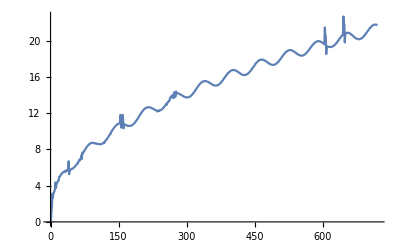

```mathematica
ListLinePlot[thetalist]
```